## Final Graph, 1964-2017, with the disconnected subgraphs removed

Evaluate the Mills Draft - Copy.nb before evaluating this .nb

1) The first graph is the “Final Graph” including all data between 1964-2017

```mathematica
graphsPerYear=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersForYear[#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
```

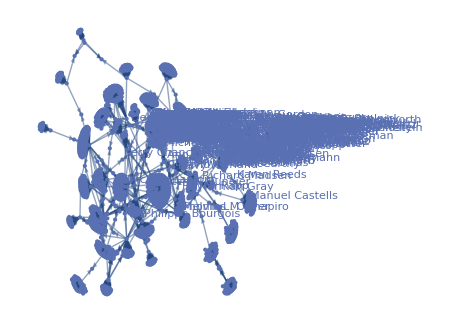

```mathematica
accumulatingGraphs=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersBetweenYears[yearsRange[[1]],#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Range@@yearsRange];
accumulatingGraphs[2017]
```

This second graph is a progression - How can I measure rates of change?

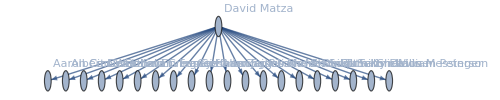
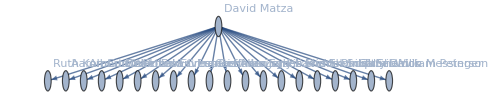
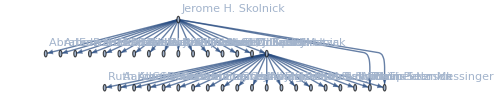
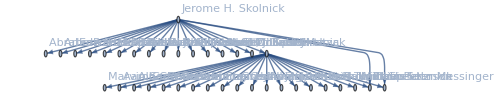
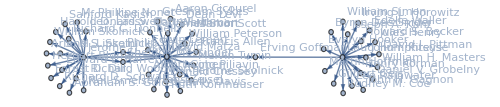
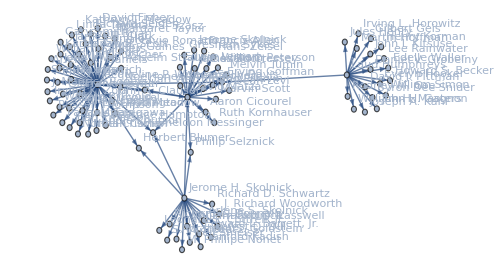
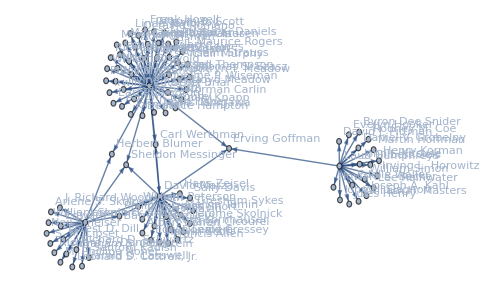
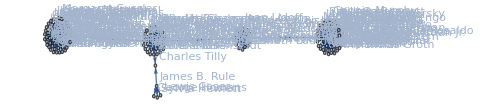
<|1964→-Graphics-,1965→-Graphics-,1966→-Graphics-,1967→-Graphics-,1968→-Graphics-,1969→-Graphics-,1970→-Graphics-,1971→-Graphics-,1972→-Graphics-,1973→-Graphics-,1974→-Graphics-,1975→-Graphics-,1976→-Graphics-,1977→-Graphics-,1978→-Graphics-,1979→-Graphics-,1980→-Graphics-,1981→-Graphics-,1982→-Graphics-,1983→-Graphics-,1984→-Graphics-,1985→-Graphics-,1986→-Graphics-,1987→-Graphics-,1988→-Graphics-,1989→-Graphics-,1990→-Graphics-,1991→-Graphics-,1992→-Graphics-,1993→-Graphics-,1994→-Graphics-,1995→-Graphics-,1996→-Graphics-,1997→-Graphics-,1998→-Graphics-,1999→-Graphics-,2000→-Graphics-,2001→-Graphics-,2002→-Graphics-,2003→-Graphics-,2004→-Graphics-,2005→-Graphics-,2006→-Graphics-,2007→-Graphics-,2008→-Graphics-,2009→-Graphics-,2010→-Graphics-,2011→-Graphics-,2012→-Graphics-,2013→-Graphics-,2014→-Graphics-,2015→-Graphics-,2016→-Graphics-,2017→-Graphics-|>

```mathematica
accumulatingGraphs
```